```mathematica
lim = 2000;
dim = 5;
```

```mathematica
data =Import["C:\\Users\\wilde\\Desktop\\Concurrency\\beerdata.csv"];
pca = data[[1;;lim]];
 style = Flatten[data[[lim+1;;2*lim]]];
ev = data[[2*lim+1;;2*lim+dim]];
```

```mathematica
pca
```

{{0.6492,0.6492,0.6492,},{0.315902,0.315902,0.315902,},1996,{0.634519,0.634519,0.634519,},{0.762695,0.762695,0.762695,}}
 |  |  |  |

```mathematica
(*Descriptors*)
```

```mathematica
descs = {"accessible","acidic","aggressive","alcoholic","almondlike/almond/almondy","apple/applelike","artificial","assertive","astringent","backbone","bacony/bacon","balance/balanced","bananalike/banana","barnyard","big","biscuity/biscuit","bitter/bitterness","body/bodied","bold","boozy/booze","bourbonlike/bourbon/bourbony","bready/bread","Brettanomyces/brett/bretty","bright","bubblegum/bubblegummy","burnt","buttery/butter","caramely/caramel","catty","chalky/chalk","cheesy/cheese","chewy","Chlorophenolic","chocolaty/chocolate/chocolatey","cigarlike/cigar","citrusy/citrus","clean","clovelike/clove/clovey","cloying","coconut/coconutty","coffeelike/coffee","colorful","complex","corked/cork/corky","cornlike/corn","crackerlike/cracker/crackery","creamy/cream","crisp/crispy","dark","deep","delicate","Diacetyl","dirty/dirt","dissipate","doughy/dough","fruity/fruit","dry","earthy/earth","estery/ester","farmlike/farm/farmy","fine","firm","flat","flowery/flower","fluffy/fluff","foamy/foam","fresh","gassy/gas","Geraniol","grainy/grain","grapefruity/grapefruit","grassy/grass","greasy/grease","green","harmonious","harsh","hazy/haze","head","hearty","heavy","herbal","highlights","hollow","honeylike/honey","hoppy/hops","horselike/horse/horsey","hot","husky","inky/ink","intense","jammy/jam","Lactobacillus","leathery/leather","legs/leggy","lemony/lemon","light","lightstruck","linalool","medicinal/medicine","mellow","melonlike/melon/melony","Mercaptan","metallic/metal","mild","milky/milk","minerally/mineral","molasses","moldy/mold","moussy","musty","nutty/nuts","oaky/oak","oatmeal","oat/oaty","oily/oil","Chlorophenol","oxidation","oxidized","papery/paper","peaty/peat","peppery/pepper","perfumy/perfume","persistent","phenolic","powerful","rancid","refined","refreshing","resinous/resin/resiny","rich","roasted/roast/roasty","robust","rocky","saccharine","salty/salt/salted","sediment/sedimenty","sharp","sherrylike/sherry","silky/silk","skunky/skunked/skunk","smoky/smoke/smoked","smooth","soapy/soap","soft","solventlike/solvent/solventy","sour/soured","spicy/spice/spiced","stale/staled","sticky","sulfidic/sulfide/sulfitic","sweet","syrupy/syrup","tannic/tannins/tannin","tart","texture/textured","thick","thin","toasty/toast/toasted","toffee","nonenal","treacle","turbid","vanilla","vegetal","viscous","warming","watery/water","winelike/winey/wine","woody/wood","worty/wort","yeasty/yeast","young","zesty/zest"};
```

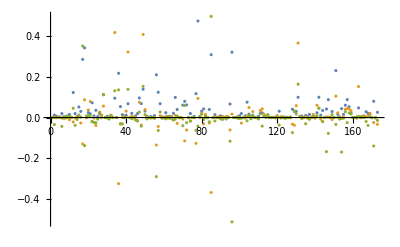

```mathematica
ListPlot[ev,PlotRange->All]
```

```mathematica
For[i=0,i≤173,i++,If[ev[[1]][[i]]>.1,Print[descs[[i]]],If[ev[[3]][[i]]<-.1,Print["-"descs[[i]]]]]]
```

balance/balanced

bitter/bitterness

body/bodied

caramely/caramel

chocolaty/chocolate/chocolatey

citrusy/citrus

dark

fruity/fruit

dry

hazy/haze

head

hoppy/hops

- lemony/lemon

light

- sour/soured

sweet

- tart

- yeasty/yeast

```mathematica
stocount = Sort[Counts[style],Greater]
```

<|India Pale Ale→587,Pale Ale→355,Stout→189,Wild/Sour Beer→124,Wheat Beer→117,Pilseners and Pale Lager→116,Specialty Beer→100,Strong Ale→89,Porter→73,Dark Lager→72,Dark Ale→62,Brown Ale→60,Bock→31,Hybrid Beer→25|>

```mathematica
stocolor = <|"India Pale Ale"->RGBColor[1,0,0,1],"Pale Ale"->RGBColor[1,0.5,0,1],"Stout"->RGBColor[0,0,1,0],"Wheat Beer"->RGBColor[0.5,1,0.5,0],"Pilseners and Pale Lager"->RGBColor[1,1,0,0],"Wild/Sour Beer"->RGBColor[0.5,0,0.5,0],"Strong Ale"->RGBColor[0.68,0.39,0,0],"Porter"->RGBColor[0,0.65,1,0],"Specialty Beer"->RGBColor[0.2,0.23,0.25,0],"Brown Ale"->RGBColor[0.43,0.26,0,0],"Dark Ale"->RGBColor[0,0,0.4,0],"Dark Lager"->RGBColor[0.48,0.5,0,0],"Bock"->RGBColor[1,0.62,0.48,0],"Hybrid Beer"->RGBColor[1,0.6,1,0]|>
```

<|India Pale Ale→RGBColor[1, 0, 0, 1],Pale Ale→RGBColor[1, 0.5, 0, 1],Stout→RGBColor[0, 0, 1, 0],Wheat Beer→RGBColor[0.5, 1, 0.5, 0],Pilseners and Pale Lager→RGBColor[1, 1, 0, 0],Wild/Sour Beer→RGBColor[0.5, 0, 0.5, 0],Strong Ale→RGBColor[0.68, 0.39, 0, 0],Porter→RGBColor[0, 0.65, 1, 0],Specialty Beer→RGBColor[0.2, 0.23, 0.25, 0],Brown Ale→RGBColor[0.43, 0.26, 0, 0],Dark Ale→RGBColor[0, 0, 0.4, 0],Dark Lager→RGBColor[0.48, 0.5, 0, 0],Bock→RGBColor[1, 0.62, 0.48, 0],Hybrid Beer→RGBColor[1, 0.6, 1, 0]|>

```mathematica
assoc = AssociationThread[pca->style];
```

```mathematica
res = FindClusters[assoc]
```

```mathematica
pcaproj[dims_]:=Table[{pca[[i]][[dims[[1]]]],pca[[i]][[dims[[2]]]],pca[[i]][[dims[[3]]]]},{i,1,lim}]
```

```mathematica
colors=Table[stocolor[style[[i]]],{i,1,lim}];
```

```mathematica
Graphics3D[Prepend[Riffle[colors,Point/@pcaproj[{2,5,4}]],PointSize[.01]],Axes->True,AxesLabel->{PC1,PC2,PC3}]
```

-Graphics3D-